\documentclass{ximera}
\input{../preamble.tex}
\author{Matthew Carr}
\license{Creative Commons 3.0 By-NC}
\begin{document}
\begin{exercise}
\outcome{Use limits to find the slope of the tangent line at a point.}
\tag{limits}
\tag{derivative}
\tag{tangent}
Let $R(v)=\frac{1}{6} (-v+\sin (v)+1)$. Find the slope $m_{tan}$, of the line tangent to $R$ at $v=-2$.


\[
 m_{tan}=\begin{prompt} = \answer{\frac{\cos (2)}{6}-\frac{1}{6}}\end{prompt}
\]
\end{exercise}
\end{document}

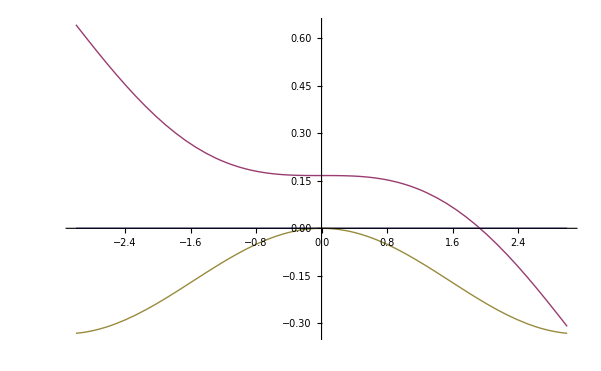

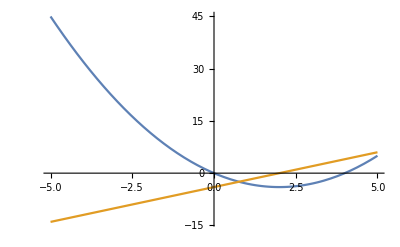

```mathematica
LaTeX[x_]:=ToString[TeXForm[x]];
(*By MVT (IVT?) w/e it is, polynomial with all real roots implies that between two roots there is a root of the derivative*)
listo={-4,-3,-2,-1,0,1,2,3,4};
listm={-4,-3,-2,-1,1,2,3,4};
wlist={1/4,1/2,1/4};
list={-1,0,1};
code:=Module[{
deg=RandomChoice[{9/50,9/50,1/10,9/50,9/50}->{-1,0,1,2,3}],
func=RandomChoice[{a,b,c,f,g,s,p,r,y,A,B,C,F,G,P,R,Y}],
variable=RandomChoice[{x,z,t,n,k,w,u,v,θ,ψ}],
pp=RandomInteger[{-5,5}],
ch=RandomChoice[{"poly","exp"}]
},

If[ch=="poly",
If[deg==-1,
gg[xx_]=(RandomChoice[listm]xx+RandomChoice[listo]);
ff[xx_]=RandomChoice[listm]/gg[xx];
,
ff[xx_]=1/15 Expand[Product[(xx-RandomChoice[listo]),{k,0,deg}]];
While[ff[xx]==0,
ff[xx_]=1/15 Expand[Product[(xx-RandomChoice[listo]),{k,0,deg}]];
];
];
];
If[ch=="exp",
ff[xx_]=1/6(Exp[1/5*RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[xx]+RandomChoice[wlist->list]Sin[xx]]+RandomChoice[wlist->list]Sin[RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[xx]+RandomChoice[wlist->list]Sin[xx]]]+RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[xx]+RandomChoice[wlist->list]Sin[xx]);
While[ff[x]==0||ff[x]==1,
ff[xx_]=1/6(Exp[1/5*RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[xx]+RandomChoice[wlist->list]Sin[xx]]+RandomChoice[wlist->list]Sin[RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[xx]+RandomChoice[wlist->list]Sin[xx]]]+RandomChoice[wlist->list]xx+RandomChoice[wlist->list]Cos[xx]+RandomChoice[wlist->list]Sin[xx]+RandomChoice[wlist->list]xx);
];
];

If[ch=="poly"&&deg==-1,
While[gg[pp]==0,
pp=RandomInteger[{-10,10}];
];
];
answer=Expand[ff'[pp]];

StringJoin["\\documentclass{ximera}
\\input{../preamble.tex}
\\author{Matthew Carr}
\\license{Creative Commons 3.0 By-NC}
\\begin{document}
\\begin{exercise}
\\outcome{Use limits to find the slope of the tangent line at a point.}
\\tag{limits}
\\tag{derivative}
\\tag{tangent}
Let $",LaTeX[func],"(",LaTeX[variable],")=",LaTeX[ff[variable]],"$. Find the slope $m_{tan}$, of the line tangent to $",LaTeX[func],"$ at $",LaTeX[variable],"=",LaTeX[pp],"$.

\n\\[\n m_{tan}=\\begin{prompt} = \\answer{",LaTeX[answer],"}\\end{prompt}
\\]
\\end{exercise}
\\end{document}\n\n"]]

StringJoin[Table[code,{1}]]
Plot[{0,ff[x],ff'[x]},{x,-3,3}]
```

```mathematica
fff'[θ]
```

-Sin[θ]+e^(-θ+Cos[Cos[θ]+Sin[θ]]) Log[e] (-1-(Cos[θ]-Sin[θ]) Sin[Cos[θ]+Sin[θ]])

```mathematica
?ToExpression
```

ToExpression[input] gives the expression obtained by interpreting strings or boxes as Wolfram Language input. 
ToExpression[input,form] uses interpretation rules corresponding to the specified form. 
ToExpression[input,form,h] wraps the head h around the expression produced before evaluating it.

```mathematica
ff[x]
```

ⅇ^(-Cos[x-Cos[x]]+Sin[x+Cos[x]+Sin[x]])+x

```mathematica
ff[x]
```

ⅇ^(x+Cos[Sin[x]]+Sin[Cos[x]+Sin[x]])+Cos[x]+Sin[x]

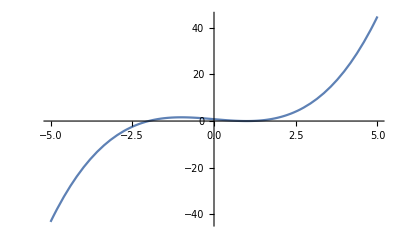

```mathematica
Plot[{ff'[x]},{x,-5,5}]
```

```mathematica
5/6
```

5/6

```mathematica
1-1/10
```

```mathematica
9/50//N
```

0.18